# Introduction to Computational Physical Chemistry

© 2017 by Joshua Schrier and University Science Books  (Version: 25 July 2017)
Publisher’s Website: http://www.uscibooks.com/schrier.htm

## Chapter 5 - Hartree-Fock Self-Consistent Field

## 5.1 HELIUM ATOM

### 5.1.1 Minimal model

```mathematica
hIntegral[zeta_]:=0.5*zeta^2-2*zeta
twoElecIntegral[zeta_]:=(5/8)*zeta
```

```mathematica
variationalEnergy[zeta_]:=2*hIntegral[zeta]+twoElecIntegral[zeta]
```

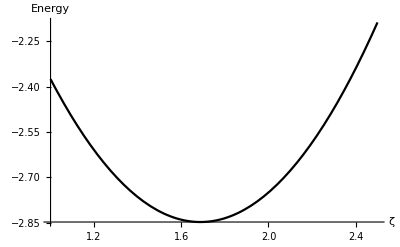

```mathematica
Plot[ variationalEnergy[zeta],{zeta,1,2.5},
AxesLabel->{"ζ","Energy"}]
```

```mathematica
soln=NMinimize[variationalEnergy[zeta],{zeta,1.6,1.8}]
```

{-2.84766,{zeta→1.6875}}

### 5.1.2 Self-consistent calculation

```mathematica
z1=1.45363;z2=2.91093;(*Basis orbital exponents*)
```

```mathematica
h11=0.5*z1^2-2*z1;(*Hamiltonian matrix elements*)
h22=0.5*z2^2-2*z2;h12=z1^(3/2)*z2^(3/2)*(4*z1*z2-8*z1-8*z2)/((z1+z2)^3);
```

```mathematica
MatrixForm[
Hmatr={{h11,h12},{h12,h22}}] (*Hamiltonian matrix*)
```

(-1.85074 | -1.88347
-1.88347 | -1.5851)

```mathematica
j1111=(5/8)*z1;
j2222=(5/8)*z2;j1122=(z1^4*z2+4*z1^3*z2^2+z1*z2^4+4*z1^2*z2^3)/((z1+z2)^4);j1212=20*z1^3*z2^3/((z1+z2)^5);j1112=(16*z1^(9/2)*z2^(3/2)/((3*z1+z2)^4))*((12*z1+8*z2)/((z1+z2)^2)+(9*z1+z2)/(2*z1^2));j1222=(16*z2^(9/2)*z1^(3/2)/((3*z2+z1)^4))*((12*z2+8*z1)/((z2+z1)^2)+(9*z2+z1)/(2*z2^2));
```

```mathematica
twoElec=Array[0,{2,2,2,2}];(*Two-electron integrals matrix*)
twoElec[[1,1,1,1]]=j1111;twoElec[[2,2,2,2]]=j2222;
twoElec[[1,1,2,2]]=j1122;twoElec[[2,2,1,1]]=j1122;
twoElec[[1,2,1,2]]=j1212;twoElec[[2,1,1,2]]=j1212;
twoElec[[1,2,2,1]]=j1212;twoElec[[2,1,2,1]]=j1212;
twoElec[[1,1,1,2]]=j1112;twoElec[[1,1,2,1]]=j1112;
twoElec[[1,2,1,1]]=j1112;twoElec[[2,1,1,1]]=j1112;
twoElec[[1,2,2,2]]=j1222;twoElec[[2,2,1,2]]=j1222;
twoElec[[2,1,2,2]]=j1222;twoElec[[2,2,2,1]]=j1222;
```

```mathematica
MatrixForm[twoElec]
```

((0.908519 | 0.906058
0.906058 | 1.18485) | (0.906058 | 0.956719
0.956719 | 1.3004)
(0.906058 | 0.956719
0.956719 | 1.3004) | (1.18485 | 1.3004
1.3004 | 1.81933))

```mathematica
s11=1.0;s22=1.0;(*Overlap matrix elements*)
s12=8*z1^(3/2)*z2^(3/2)/((z1+z2)^3);
MatrixForm[
Smatr={{s11,s12},{s12,s22}}] (*Overlap matrix*)
```

(1. | 0.837524
0.837524 | 1.)

```mathematica
MatrixForm[
Xmatr=MatrixPower[Smatr,-1/2]] (*Transform to orthogonal basis*)
```

(1.60929 | -0.871584
-0.871584 | 1.60929)

```mathematica
coeff={{0,0},{0,0}};(*initialize wavefunction coefficients to zero*)

MatrixForm[Fmatr=Table[Hmatr[[r,s]]+(*build initial Fock matrix*)Sum[coeff[[1,t]]*coeff[[1,u]]*twoElec[[r,s,t,u]],{t,1,2},{u,1,2}],{r,1,2},{s,1,2}]]
```

(-1.85074 | -1.88347
-1.88347 | -1.5851)

```mathematica
{evals,coeff}=Eigensystem[ConjugateTranspose[Xmatr].Fmatr.Xmatr]
```

{{-1.97962,1.03859},{{-0.76193,-0.647659},{0.647659,-0.76193}}}

```mathematica
Do[coeff[[i]]=Xmatr.coeff[[i]],{i,1,2}] (*transform eigenvectors*)
```

```mathematica
MatrixForm[Fmatr=Table[Hmatr[[r,s]]+(*rebuild Fock matrix*)Sum[coeff[[1,t]]*coeff[[1,u]]*twoElec[[r,s,t,u]],{t,1,2},{u,1,2}],{r,1,2},{s,1,2}]]
```

(-0.830055 | -0.821978
-0.821978 | -0.155333)

```mathematica
coeff={{0,0},{0,0}};(*initialize wavefunction coefficients to zero*)

Do[(*perform SCF loop*)
Fmatr=Table[Hmatr[[r,s]]+
Sum[coeff[[1,t]]*coeff[[1,u]]*twoElec[[r,s,t,u]],{t,1,2},{u,1,2}],{r,1,2},{s,1,2}];{evals,coeff}=Eigensystem[ConjugateTranspose[Xmatr].Fmatr.Xmatr];Do[coeff[[i]]=Xmatr.coeff[[i]],{i,1,2}];
sortEigen=Ordering[evals];(*find ordering that sorts eigenvalues*)
evals=evals[[sortEigen]];(*sort eigenvalues*)
coeff=coeff[[sortEigen]];(*sort eigenvectors*)
,{iterations,10}]
```

Erratum (first printing):  p .110-- The second term in the output of evals, is incorrect.The first output on this page should read :

```mathematica
evals
```

{-0.917935,2.05685}

```mathematica
coeff[[1]]
```

{-0.843785,-0.180687}

```mathematica
2*(Sum[coeff[[1,r]]*Hmatr[[r,s]]*coeff[[1,s]],{r,1,2},{s,1,2}])+Sum[(*(ψψ|ψψ)*)
coeff[[1,r]]*coeff[[1,s]]*coeff[[1,t]]*coeff[[1,u]]*twoElec[[r,s,t,u]],{r,1,2},{s,1,2},{t,1,2},{u,1,2}]
```

-2.86167

### 5.1.3 Generalization to many-electron systems

```mathematica
buildPmatr[coeff_]:=Table[
2*Sum[coeff[[i,t]]*coeff[[i,u]],{i,1,nOcc}],
{t,1,nBasis},{u,1,nBasis}]
```

```mathematica
buildFmatr[thisPmatr_]:=Module[{newFmatr=Hmatr},(*initialize*)Do[newFmatr[[r,s]]+=(*add electron interaction terms*)thisPmatr[[t,u]]*(twoElec[[r,s,t,u]]-0.5*twoElec[[r,u,t,s]]);,{r,1,nBasis},{s,1,nBasis},{t,1,nBasis},{u,1,nBasis}];
newFmatr (*return the new Fock matrix*)
];
```

```mathematica
calcHFenergy[sortedEvals_,thisPmatr_,Vnn_]:=Sum[sortedEvals[[i]],{i,1,nOcc}]+0.5*Sum[thisPmatr[[r,s]]*Hmatr[[r,s]],{r,1,nBasis},{s,1,nBasis}]+Vnn
```

```mathematica
nBasis=2;(*number of basis functions*)
nOcc=1;(*number of doubly occupied molecular orbitals*)
(*Hmatr,Smatr,Xmatr,twoElec all defined in previous example*)
coeff={{0,0},{0,0}};(*an arbitrary initial guess*)
Pmatr=buildPmatr[coeff];(*initialize charge density matrix*)
Do[(*SCF procedure*)
Fmatr=buildFmatr[Pmatr];{evals,coeff}=Eigensystem[ConjugateTranspose[Xmatr].Fmatr.Xmatr];
Do[
coeff[[i]]=Xmatr.coeff[[i]],{i,1,nBasis}];(*transform eigenvectors*)
sortEigen=Ordering[evals];(*find ordering that sorts eigenvalues*)
evals=evals[[sortEigen]];(*sort eigenvalues*)
coeff=coeff[[sortEigen]]; (*sort eigenvectors*)
Pmatr=buildPmatr[coeff];(*new charge density from new eigenvecs*)

Print["iteration: ",iteration," energy = ",calcHFenergy[evals,Pmatr,0]];
,{iteration,10}]
```

iteration: 1 energy = -3.95924

iteration: 2 energy = -2.78457

iteration: 3 energy = -2.8586

iteration: 4 energy = -2.86152

iteration: 5 energy = -2.86167

iteration: 6 energy = -2.86167

iteration: 7 energy = -2.86167

iteration: 8 energy = -2.86167

iteration: 9 energy = -2.86167

iteration: 10 energy = -2.86167

## 5.2 HYDROGEN MOLECULE

### 5.2.1 Gaussian orbitals

```mathematica
g1sUnnorm[alpha_,rA_]:=Exp[-alpha*(rA.rA)];g1sNormConst[alpha_]:=(2*alpha/Pi)^(3/4);g1s[alpha_,rA_]:=g1sNormConst[alpha]*g1sUnnorm[alpha,rA];
```

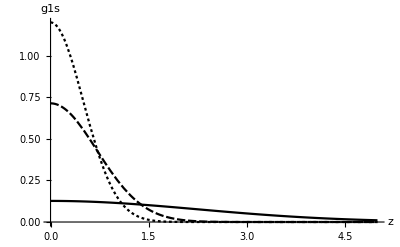

```mathematica
Plot[{g1s[0.1,{0,0,z}],g1s[1.0,{0,0,z}],g1s[2.0,{0,0,z}]},
{z,0,5},PlotRange->All,AxesLabel->{"z","g1s"}]
```

```mathematica
propK[alpha_,rA_,beta_,rB_]:=Exp[-alpha*beta*((rA-rB).(rA-rB))/(alpha+beta)];
rP[alpha_,rA_,beta_,rB_]:=(alpha*rA+beta*rB)/(alpha+beta);p[alpha_,beta_]:=alpha+beta;
```

### 5.2.2 Integral evaluation

```mathematica
overlapInt[alpha_,rA_,beta_,rB_]:=g1sNormConst[alpha]*g1sNormConst[beta]*propK[alpha,rA,beta,rB]*(Pi/(alpha+beta))^(3/2)
```

```mathematica
kineticEnInt[alpha_,rA_,beta_,rB_]:=g1sNormConst[alpha]*g1sNormConst[beta]*propK[alpha,rA,beta,rB]*(((alpha*beta)/(alpha+beta))*(3-(2*alpha*beta*((rA-rB).(rA-rB))/(alpha+beta))))*(Pi/(alpha+beta))^(3/2);
```

```mathematica
f0func[t_]:=Erf[(t+10^-10)^(1/2)]*((Pi/(t+10^-10))^(1/2))/2
```

```mathematica
nuclearInt[alpha_,rA_,beta_,rB_,Zc_,rC_]:=(-Zc)*g1sNormConst[alpha]*
g1sNormConst[beta]*propK[alpha,rA,beta,rB]*(2*π/(alpha+beta))*f0func[(alpha+beta)*((rP[alpha,rA,beta,rB]-rC).(rP[alpha,rA,beta,rB]-rC))]
```

Erratum (first printing):  p. 119 — In definition of twoElecInt[], the first propK[] function is missing the closing “]”.  The function should read:

```mathematica
twoElecInt[alpha_,rA_,beta_,rB_,gamma_,rC_,delta_,rD_]:=propK[alpha,rA,beta,rB]*propK[gamma,rC,delta,rD]*g1sNormConst[alpha]*g1sNormConst[beta]*g1sNormConst[gamma]*g1sNormConst[delta]*((2 π^(5/2))/((alpha+beta)*(gamma+delta)*(alpha+beta+gamma+delta)^(1/2)))*f0func[(alpha+beta)*(gamma+delta)*((rP[alpha,rA,beta,rB]-rP[gamma,rC,delta,rD]).(rP[alpha,rA,beta,rB]-rP[gamma,rC,delta,rD]))/(alpha+beta+gamma+delta)]
```

### 5.2.4 Organizing atomic and basis set data

```mathematica
nAtom=2;(*number of atoms*)
nBasis=2;(*total number of basis functions*)
nOcc=1;(*number of occupied molecular orbitals*)
atomPos={{0,0,0},{0,0,1.6}};(*xyz coordinates of the nuclei*)
atomZ={1,1};(*atomic numbers of the nuclei*)
basisPos={{0,0,0},{0,0,1.6}};(*atom-centered basis functions*)
basisOrb={0.4166,0.4166};(*orbital exponents of each basis function*)
```

```mathematica
MatrixForm[Smatr=Table[overlapInt[basisOrb[[r]],basisPos[[r]],basisOrb[[s]],basisPos[[s]]],{r,1,nBasis},{s,1,nBasis}]]
```

(1. | 0.586696
0.586696 | 1.)

```mathematica
MatrixForm[Xmatr=MatrixPower[Smatr,-1/2]]
```

(1.17468 | -0.380803
-0.380803 | 1.17468)

```mathematica
MatrixForm[Hmatr=Table[
kineticEnInt[basisOrb[[r]],basisPos[[r]],basisOrb[[s]],basisPos[[s]]]+Sum[nuclearInt[basisOrb[[r]],basisPos[[r]],basisOrb[[s]],basisPos[[s]],atomZ[[c]],atomPos[[c]]],{c,1,nAtom}]
,{r,1,nBasis},{s,1,nBasis}]]
```

(-1.00578 | -0.787878
-0.787878 | -1.00578)

```mathematica
MatrixForm[twoElec=Table[
twoElecInt[basisOrb[[r]],basisPos[[r]],basisOrb[[s]],basisPos[[s]],basisOrb[[t]],basisPos[[t]],basisOrb[[u]],basisPos[[u]]],
{r,1,nBasis},{s,1,nBasis},{t,1,nBasis},{u,1,nBasis}]]
```

((0.728307 | 0.392174
0.392174 | 0.534901) | (0.392174 | 0.250693
0.250693 | 0.392174)
(0.392174 | 0.250693
0.250693 | 0.392174) | (0.534901 | 0.392174
0.392174 | 0.728307))

### 5.2.5 Functions for the total Hartree-Fock energy

```mathematica
Vnn=Sum[atomZ[[c]]*atomZ[[cp]]/Norm[atomPos[[c]]-atomPos[[cp]]]
,{cp,2,nAtom},{c,1,cp-1}]
```

0.625

### 5.2.6 Performing the SCF calculation

```mathematica
coeff={{0,0},{0,0}};(*an arbitrary initial guess*)
Pmatr=buildPmatr[coeff];(*initialize charge density matrix*)
Do[(*SCF procedure*)
Fmatr=buildFmatr[Pmatr];
{evals,coeff}=Eigensystem[ConjugateTranspose[Xmatr].Fmatr.Xmatr];
Do[coeff[[i]]=Xmatr.coeff[[i]],{i,1,nBasis}];(*transform eigenvectors*)

sortEigen=Ordering[evals];(*find ordering that sorts eigenvalues*)
evals=evals[[sortEigen]];(*sort eigenvalues*)
coeff=coeff[[sortEigen]];(*sort eigenvectors*)
Pmatr=buildPmatr[coeff];(*new charge density from new eigenvecs*)
Print["iteration: ",iteration,"   energy = ",calcHFenergy[evals,Pmatr,Vnn]];
,{iteration,10}]
```

iteration: 1   energy = -1.63587

iteration: 2   energy = -0.973876

iteration: 3   energy = -0.973876

iteration: 4   energy = -0.973876

iteration: 5   energy = -0.973876

iteration: 6   energy = -0.973876

iteration: 7   energy = -0.973876

iteration: 8   energy = -0.973876

iteration: 9   energy = -0.973876

iteration: 10   energy = -0.973876

### 5.2.7 Bond dissociation curve

```mathematica
nAtom=2;nBasis=2;nOcc=1;atomZ={1,1};basisOrb={0.4166,0.4166};
dataPoints={};
Do[
(*set the current internuclear distance*)
atomPos={{0,0,0},{0,0,dist}};
basisPos={{0,0,0},{0,0,dist}};

(*compute the matrices at this value of internuclear distance*)Smatr=Table[overlapInt[basisOrb[[r]],basisPos[[r]],basisOrb[[s]],basisPos[[s]]],{r,1,nBasis},{s,1,nBasis}];
Xmatr=MatrixPower[Smatr,-1/2];
Hmatr=Table[
kineticEnInt[basisOrb[[r]],basisPos[[r]],basisOrb[[s]],basisPos[[s]]]+
Sum[
nuclearInt[basisOrb[[r]],basisPos[[r]],
basisOrb[[s]],basisPos[[s]],atomZ[[c]],atomPos[[c]]],
{c,1,nAtom}],
{r,1,nBasis},{s,1,nBasis}];
twoElec=Table[
twoElecInt[basisOrb[[r]],basisPos[[r]],basisOrb[[s]],basisPos[[s]],basisOrb[[t]],basisPos[[t]],basisOrb[[u]],basisPos[[u]]],
{r,1,nBasis},{s,1,nBasis},{t,1,nBasis},{u,1,nBasis}];

(*nuclear-nuclear interaction has changed too*)Vnn=Sum[atomZ[[c]]*atomZ[[cp]]/Norm[atomPos[[c]]-atomPos[[cp]]],{cp,2,nAtom},{c,1,cp-1}];

(*perform SCF calculation at this distance*)
coeff={{0,0},{0,0}};Pmatr=buildPmatr[coeff];

Do[(*SCF procedure*)
Fmatr=buildFmatr[Pmatr];{evals,coeff}=Eigensystem[ConjugateTranspose[Xmatr].Fmatr.Xmatr];
Do[coeff[[i]]=Xmatr.coeff[[i]],{i,1,nBasis}];sortEigen=Ordering[evals];evals=evals[[sortEigen]];coeff=coeff[[sortEigen]];Pmatr=buildPmatr[coeff];
,{iteration,10}];(*end SCF loop*)

(*add the current distance and SCF energy to our list*)AppendTo[dataPoints,{dist,N[calcHFenergy[evals,Pmatr,Vnn]]}];

,{dist,0.1,10.0,0.01}];(*end loop over internuclear distances*)
```

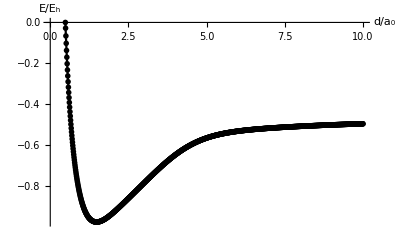

```mathematica
ListPlot[dataPoints,Joined->True,AxesLabel->{"d/a_0","E/E_h"}]
```

```mathematica
Position[dataPoints,Min[dataPoints]] (*find lowest-energy entry*)
```

{{139,2}}

```mathematica
dataPoints[[139]] (*display that entry---a {position,energy} tuple*)
```

{1.48,-0.977196}

```mathematica
dataPoints[[139,1]]*0.52917 (*convert internuclear distance to angstroms*)
```

0.783172